```mathematica
Predicting Bitcoin Bubbles
```

## References

- Transaction Dynamics of Blockchain and Predictable Bitcoin Bubbles. - https://polybox.ethz.ch/index.php/s/LzLmTZXzqF8rCAs

- Are Bitcoin Bubbles Predictable? Combining a Generalized Metcalfe’s Law and the LPPLS Model. - https://arxiv.org/pdf/1803.05663.pdf

- Metcalfe's law.

## Resources

- Bitcoin active addresses: bitinfocharts.com.

- Bitcoin market capitalization: bitinfocharts.com.

- Bitcoin hourly price: Recent (2024) data - bitstamp.com.

- Bitcoin circulating supply: https://www.blockchain.com/charts/total-bitcoins.

## In This Notebook

LPPLS model implementation (2024 ed.).

```mathematica
base=DirectoryName[NotebookFileName[]];
firstPriceDate="2018-05-15"
lastPriceDate=DateString[Yesterday,"ISODate"]
```

2018-05-15

2025-12-24

```mathematica
hourlyPricesUrl="https://www.cryptodatadownload.com/cdd/Bitstamp_BTCUSD_1h.csv";
prices =Import[hourlyPricesUrl, HeaderLines->1]
```

```mathematica
(* Some freshness checks: *)
lastDownloadedDateTime=prices[[2]][[2]];
{lastDownloadedDate, lastDownloadedTime}=StringSplit[lastDownloadedDateTime]
{DateString[DatePlus[lastDownloadedDate, -1], "ISODate"]==lastPriceDate, lastDownloadedTime=="00:00:00"}
```

{2025-03-30,00:00:00}

{True,True}

```mathematica
closingPrices={#[[1]],#[[7]]}&/@prices
```

```mathematica
(* Filter non-numerical values *)
closingPricesFilter=Select[closingPrices, NumberQ[#[[2]]]&]
```

```mathematica
(* Hourly data *)
hourlyPrices=SortBy[closingPricesFilter, First]
```

```mathematica
Length[hourlyPrices]
```

60259

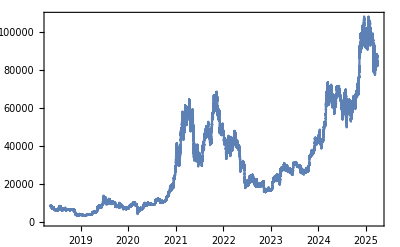

```mathematica
DateListPlot[hourlyPrices,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
Export[base<>"Bitcoin_price-hourly-"<>StringDelete[firstPriceDate, "-"]<>"-"<>StringDelete[lastPriceDate, "-"]<>".csv",hourlyPrices]
```

/Users/mauro/Projects/Bitcoin/Bitcoin_price-hourly-20180515-20250329.csv

```mathematica
(* Prices list. Pre-processed for performance: *)
hourlyPricesList = Import[base<>"Bitcoin_price-hourly-"<>StringDelete[firstPriceDate, "-"]<>"-"<>StringDelete[lastPriceDate, "-"]<>".csv"]
```

```mathematica
(* Convert to market capitalization, using circulating supply data, from blockchain.info *)
(* Load circulating supply data: https://www.blockchain.com/charts/total-bitcoins *)
supplyJsonData = Import["https://api.blockchain.info/charts/total-bitcoins?timespan=all&sampled=true&metadata=false&daysAverageString=1d&cors=true&format=json"];
```

```mathematica
supplyJson=supplyJsonData[[6]][[2]]
```

```mathematica
supplyTs=supplyJson[[All, 1]][[All,2]];
supplyQuantity=supplyJson[[All, 2]][[All,2]];
```

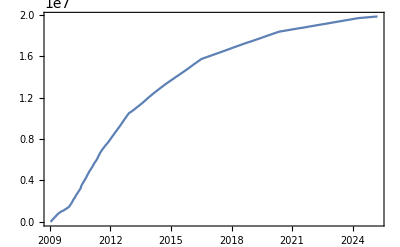

```mathematica
supplyTimestamps=MapThread[{#1, #2}&,{supplyTs, supplyQuantity}];
DateListPlot[supplyTimestamps,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Create an interpolating function from it *)
supplyFunction=Block[{},Off[ InterpolatingFunction::dmval];Interpolation[supplyTimestamps]]
```

InterpolatingFunction[…]

```mathematica
{supplyTimestamps[[1]][[1]], supplyTimestamps[[-1]][[1]]}
```

{1231568277,1743019256}

```mathematica
{hourlyPricesList[[1]][[1]],hourlyPricesList[[-1]][[1]]}
```

{1526364000,1743292800}

```mathematica
{supplyFunction[hourlyPricesList[[1]][[1]]], supplyFunction[hourlyPricesList[[-3]][[1]]]}
```

{1.70344×10^7,1.98438×10^7}

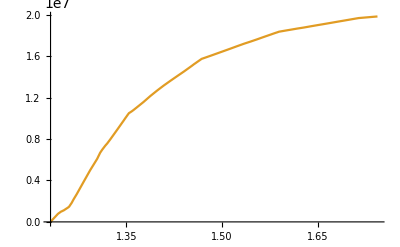

```mathematica
Plot[{,supplyFunction[i]}, {i, supplyTimestamps[[1]][[1]], supplyTimestamps[[-1]][[1]]}]
```

```mathematica
(* Generate hourly market capitalization data *)
hourlyMarketCap={#[[1]], #[[2]]*supplyFunction[#[[1]]]}&/@hourlyPricesList
```

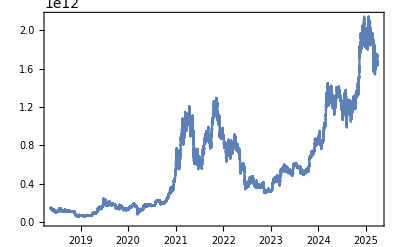

```mathematica
DateListPlot[hourlyMarketCap, DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Use the Log Market Cap *)
logMarketCap= {#[[1]], Log[#[[2]]]}&/@hourlyMarketCap
```

```mathematica
(* Appendix 5.1. Example: Analyze / predict the 2024 bubble turning point: *)
(* Generalized to multiple bubbles *)
bubblesDate={{"2023-01-01", lastPriceDate},{"2024-08-05", lastPriceDate}, {"2025-03-10", lastPriceDate}}
```

{{2023-01-01,2025-03-29},{2024-08-05,2025-03-29},{2025-03-10,2025-03-29}}

```mathematica
bubbleN=Length[bubblesDate]
```

3

```mathematica
(* Timestamp indexes: *)
bubblesTimestampIndex={UnixTime[#[[1]]], UnixTime[#[[2]]]}&/@bubblesDate
```

{{1672524000,1743199200},{1722808800,1743199200},{1741557600,1743199200}}

```mathematica
bubblesDays=(#[[2]]-#[[1]])/86400&/@bubblesTimestampIndex
```

{818,236,19}

```mathematica
bubbles=Table[Select[logMarketCap,bubblesTimestampIndex[[i]][[1]]≤#[[1]]≤ bubblesTimestampIndex[[i]][[2]]&], {i, bubbleN}];
#[[1]]&/@bubbles
```

{{1672524000,26.4845},{1722808800,27.7781},{1741557600,28.0963}}

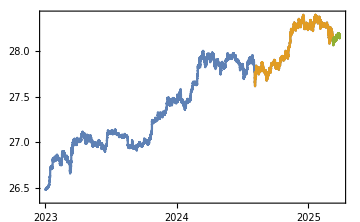

```mathematica
DateListPlot[bubbles, ImageSize->Medium, DateFunction->(FromUnixTime[#]&)]
```

```mathematica
(* Scale data horizontally and vertically *)
scaleH[data_]:= Module[{peaks, first},
(* Scale bubbles horizontally (0-1) (set 1 at the true peaks) *)
peaks=MaximalBy[data, Last][[1]];
first = data[[1]];
{(#[[1]]-first[[1]])/(peaks[[1]]-first[[1]]),#[[2]]}&/@data
]
```

```mathematica
scaleV[data_]:= Module[{min, max},
(* Rescale vertically *)
min=Min[Last /@data];
max=Max[Last /@data];
{#[[1]],(#[[2]]-min)/(max-min)}&/@data
]
```

```mathematica
bubblesScaled=scaleV[scaleH[#]]&/@ bubbles//N;
#[[-1]]&/@bubblesScaled
```

{{1.1414,0.87085},{1.75248,0.68368},{1.2809,0.643325}}

```mathematica
Length/@bubblesScaled
```

{19633,5665,457}

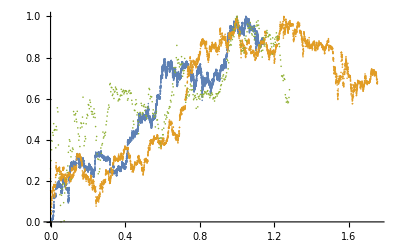

```mathematica
(* LPPLS model over the scaled bubbles: *)
(* Step 1. Identify initial error model: *)
(* 1.a Fit the log market cap with a flexible nonparametric curve. *)
ListPlot[bubblesScaled]
```

```mathematica
(* Export bubbles data: *)
bubbleScaledCsvs=MapIndexed[Export[base<>"bubbleScaled-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,bubblesScaled]
```

{/Users/mauro/Projects/Bitcoin/bubbleScaled-1.tsv,/Users/mauro/Projects/Bitcoin/bubbleScaled-2.tsv,/Users/mauro/Projects/Bitcoin/bubbleScaled-3.tsv}

```mathematica
(* Get params from R: *)
bestBandwidth=.
(*bestSpan=0.088*)
bestSpan=0.08 * 4/3
```

0.106667

```mathematica
rInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@bubbleScaledCsvs;
```

```mathematica
rRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@rInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
rParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@rRuns
```

{{14.6897,19613.6},{14.6979,5645.62},{14.9581,437.321}}

```mathematica
(* {RSS, SE, SE of the fit}: *)
rErrors=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-6;;;;2]]&/@rRuns
```

{{14.9196,0.0275809,0.000717761},{7.23453,0.0357999,0.00174188},{1.57496,0.060072,0.0103343}}

```mathematica
(* Use Loess: *)
LoessR=ResourceFunction["Loess"]
```

```mathematica
bestFits = LoessR[#, Scaled[bestSpan], #[[All, 1]], {InterpolationOrder-> 1}]&/@bubblesScaled;
```

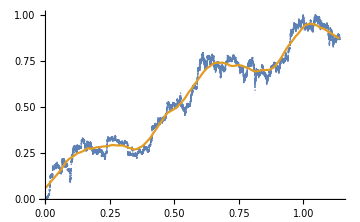
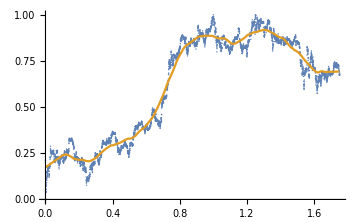
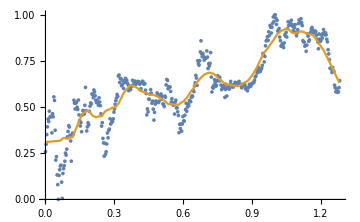

```mathematica
Show[ListPlot[#, ImageSize->Medium],   ListLinePlot[{{{0,0}},Table[{t, LoessR[#, Scaled[bestSpan], t ]}, {t, Min[#[[All, 1]]], Max[#[[All, 1]]], .005}]}]]&/@bubblesScaled
```

```mathematica
(* 1.b Detrend: *)
ℛs = Table[bubblesScaled[[i]][[All,2]]-bestFits[[i]], {i, bubbleN}];
```

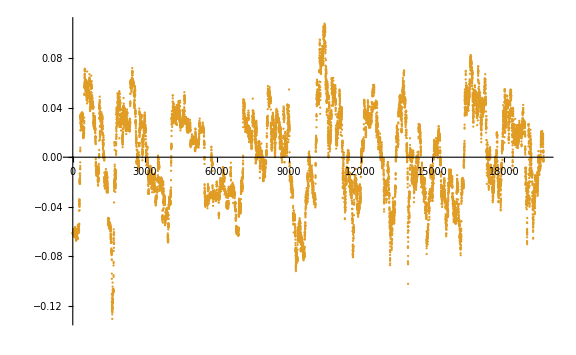
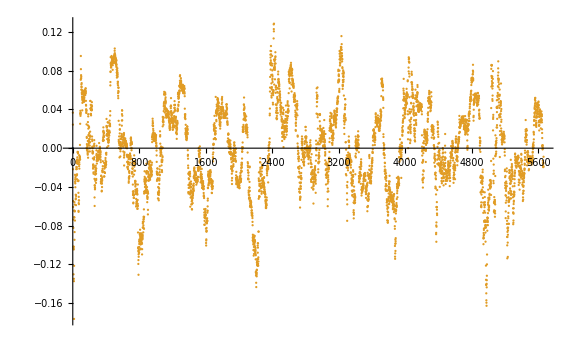
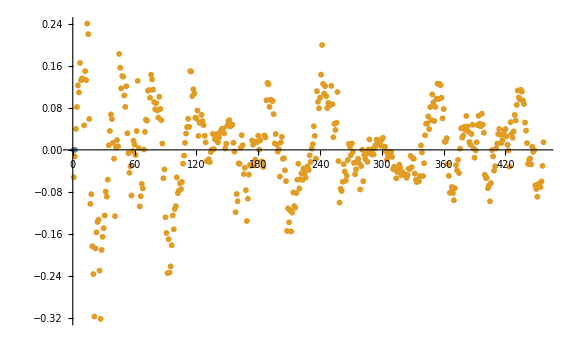

```mathematica
(* Plot residuals: *)
ListPlot[{{0,0},#}, ImageSize->Large]&/@ℛs
```

```mathematica
(* Standard deviations: *)
stdDevℛs=StandardDeviation /@ℛs
```

{0.0360741,0.0438549,0.0784405}

```mathematica
(* Standardized residuals: *)
stdℛs = MapThread[#1/#2&,{ℛs, stdDevℛs}];
```

```mathematica
(* RSS: *)
ℛsSS =Total[#^2]&/@ℛs
```

{25.5848,10.8948,2.80698}

```mathematica
(* Larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[1]]]&,{ℛsSS,rErrors}]
```

{25.5848 > 14.9196,10.8948 > 7.23453,2.80698 > 1.57496}

```mathematica
(* Residual Standard Error(s): *)
ℛsSEs=MapThread[√(Total[#1^2]/(Length[#1]-#2[[1]]))&,{ℛs,rParams}]
```

{0.0361127,0.043911,0.0796871}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0361127 > 0.0275809,0.043911 > 0.0357999,0.0796871 > 0.060072}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(Length[#1]-#2[[1]]))&,{ℛs,rParams, rErrors}]
```

{0.027577,0.0357824,0.0596902}

```mathematica
ℛsSEs=MapThread[√(Total[#1^2]/(#2[[2]]))&,{ℛs,rParams}]
```

{0.0361171,0.0439292,0.0801161}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0361171 > 0.0275809,0.0439292 > 0.0357999,0.0801161 > 0.060072}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(#2[[2]]))&,{ℛs,rParams, rErrors}]
```

{0.0275803,0.0357972,0.0600115}

```mathematica
(* 3. Fit LPPLS function: *)
tc=.
numParams=7;
lpplsModel=a +(tc-ti)^m(b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Select first bubble: *)
bubble=1
```

```mathematica
(* Select last bubble: *)
bubble=Length[bubbles]
```

3

```mathematica
(* Use the selected bubble: *)
bubbleScaled=bubblesScaled[[bubble]];
```

```mathematica
(* Use the params for the selected bubble: *)
{estimatedNParams, effectiveDfs}=rParams[[bubble]]
```

{14.9581,437.321}

```mathematica
(* Profiling over 0.1 < m < 0.9, 5 < ω < 15 and 1. < tc < 3 months in the future *)
minM=0.1;
maxM=1;
minω=3;
maxω=14;
months=1;
```

```mathematica
(* Try to estimate all the params using log-likelihood: *)
(* Define `months` in the future scaled interval endpoint: *)
bubbleScaled[[-1]][[1]]
maxTc=bubbleScaled[[-1]][[1]]+(bubblesDays[[bubble]]+30 months)/bubblesDays[[bubble]]//N
```

1.2809

3.85985

```mathematica
(* Define 2 days resolution scaled interval step: *)
stepTc=2/bubblesDays[[bubble]]//N
```

0.105263

```mathematica
(* Define 2 days resolution scaled initial time step *)
stepTi=2/bubblesDays[[bubble]]//N
```

0.105263

```mathematica
(* Slow. Shortcut below *)
fits=Table[m=.;tc=.;
bestFit=MaximalBy[Flatten[ParallelTable[{tc,m,ω,nlm=NonlinearModelFit[Select[bubbleScaled,#[[1]]>= t1&],lpplsModel,{a,b,c,d}, ti];nlm["BestFitParameters"],
ℛ=nlm["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
RSS=Total[ℛ^2],
RSS/(Length[ℛ]-numParams),
StandardDeviation[ℛ],
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,minM,maxM,1./10}, {ω,minω,maxω,1./10},  {tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],2], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[4]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]], ω-> bestFit[[3]], RSS-> bestFit[[6]],ℛerror-> bestFit[[7]], ℛσ-> bestFit[[8]],LL-> bestFit[[9]]},bestFit[[5]]], {t1, Range[0,1/2+stepTi, stepTi]}]//AbsoluteTiming
```

{753.096,{{a→7.14666,b→-6.2509,c→-0.0496304,d→0.0618448,T_1→0.,tc→2.22837,m→0.1,ω→14.,RSS→4.91607,ℛerror→0.0109246,ℛσ→0.103831,LL→844.919,ρ→0.926335,σ→-0.0390704,μ→-6.01128×10^-17},{a→1.16057,b→-0.478139,c→-0.161852,d→-0.0578409,T_1→0.105263,tc→1.49153,m→0.1,ω→3.,RSS→3.85375,ℛerror→0.00935376,ℛσ→0.0960182,LL→820.493,ρ→0.930718,σ→-0.0350756,μ→1.65586×10^-17},{a→0.418348,b→0.317446,c→-0.207833,d→-0.0368852,T_1→0.210526,tc→1.49153,m→0.1,ω→3.,RSS→3.30643,ℛerror→0.00881713,ℛσ→0.0931573,LL→795.39,ρ→0.946096,σ→-0.0301328,μ→1.52903×10^-17},{a→0.942361,b→-0.19833,c→-0.137628,d→0.132789,T_1→0.315789,tc→1.38626,m→0.1,ω→3.,RSS→2.03345,ℛerror→0.00603396,ℛσ→0.0769962,LL→732.602,ρ→0.927523,σ→-0.0287367,μ→3.37299×10^-17},{a→1.04266,b→-0.311323,c→-0.13923,d→0.123527,T_1→0.421053,tc→1.38626,m→0.1,ω→3.,RSS→2.00245,ℛerror→0.00667484,ℛσ→0.0808947,LL→643.286,ρ→0.92928,σ→-0.0298318,μ→-2.28894×10^-17},{a→0.953694,b→-0.204332,c→-0.11599,d→0.14564,T_1→0.526316,tc→1.38626,m→0.1,ω→3.1,RSS→1.8951,ℛerror→0.0072332,ℛσ→0.0840908,LL→572.833,ρ→0.9389,σ→-0.0288894,μ→1.71226×10^-17}}}

```mathematica
(* Shortcut: *)
fits=;
```

```mathematica
(* Timing in minutes: *)
fits[[1]]/60
```

12.5516

```mathematica
fits=fits[[2]];
```

```mathematica
fits[[All,{5,6,11,12}]]//TableForm
```

T_1→0. | tc→2.22837 | ℛσ→0.103831 | LL→844.919
T_1→0.105263 | tc→1.49153 | ℛσ→0.0960182 | LL→820.493
T_1→0.210526 | tc→1.49153 | ℛσ→0.0931573 | LL→795.39
T_1→0.315789 | tc→1.38626 | ℛσ→0.0769962 | LL→732.602
T_1→0.421053 | tc→1.38626 | ℛσ→0.0808947 | LL→643.286
T_1→0.526316 | tc→1.38626 | ℛσ→0.0840908 | LL→572.833

```mathematica
(* Average tc: *)
meanTc=Total[fits[[All,6]][[All,2]]]/Length[fits]
```

1.5617

```mathematica
minTc=Min[fits[[All,6]][[All,2]]]
maxTc=Max[fits[[All,6]][[All,2]]]
```

1.38626

2.22837

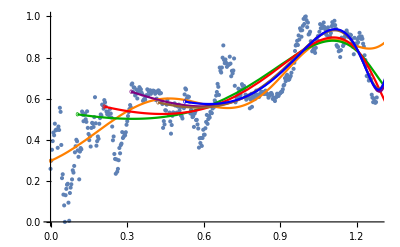

```mathematica
(* Plot of the results: *)
colors={Orange,Darker[Green],Red, Purple, Brown, Blue, Darker[Orange], Magenta,Black, Lighter[Gray], Lighter[Green], Lighter[Red], Lighter[Purple], Lighter[Brown], Lighter[Blue],Lighter[Orange]};
circles=Table[{colors[[Mod[i, Length[colors]]+1]],Thickness[0.0012],Circle[{i stepTi,lpplsModel/.fits[[i+1]]/.ti-> i stepTi},{0.005,0.0085}]}, {i, 0,Length[fits]-1}];
Show[ListPlot[bubbleScaled, ImageSize->Full, Epilog-> circles], Plot[Table[If[ti>i stepTi,Evaluate[lpplsModel/.fits[[i+1]]],""], {i,0,Length[fits]-1}], {ti, 0, maxTc}, PlotStyle->colors, Evaluated->True]]
```

```mathematica
(* Rejection criteria: See if the (standardized) residuals of the fits (ℛerror field divided by ℛσ) are below the 95% of the simulated (standardized) RSSs: *)
T1s=Subscript[T, 1]/.fits
ℛerrors=ℛerror/.fits
RSSs=RSS/.fits
ℛσs=ℛσ/.fits
```

{0.,0.105263,0.210526,0.315789,0.421053,0.526316}

{0.0109246,0.00935376,0.00881713,0.00603396,0.00667484,0.0072332}

{4.91607,3.85375,3.30643,2.03345,2.00245,1.8951}

{0.103831,0.0960182,0.0931573,0.0769962,0.0808947,0.0840908}

```mathematica
Export[base<>"t1s.tsv", Join[{{"t1"}},T1s]]
```

/Users/mauro/Projects/Bitcoin/t1s.tsv

```mathematica
(* Only last bubble *)
npBestFit=bestFits[[bubble]];
```

```mathematica
nPℓ=Length[npBestFit];
nPℓ
```

457

```mathematica
(* Plot of the residuals of the non-parametric fit vs the residuals of the parametric fit: *)
(* Non-parametric residuals: *)
npℛs=ℛs[[bubble]];
```

```mathematica
(* Parametric residuals: *)
fullFit[t_]:=lpplsModel/.fits[[1]]/.ti-> t
pℛs=Table[bubbleScaled[[i]][[2]]-fullFit[bubbleScaled[[i]][[1]]],{i,1,Length[bubbleScaled]}];
```

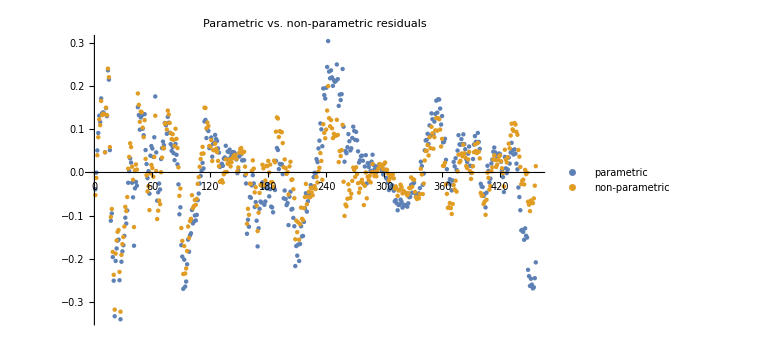

```mathematica
ListPlot[{pℛs,npℛs}, ImageSize->Large, {PlotLabel-> "Parametric vs. non-parametric residuals", PlotLegends->{"parametric","non-parametric"}}]
```

```mathematica
(* RSSs: *)
Total[#^2]&/@{npℛs, pℛs}
```

{2.80698,4.91607}

```mathematica
(* Residual Standard Errors: *)
{√(Total[npℛs^2]/effectiveDfs),√(Total[pℛs^2]/(Length[pℛs]-numParams)) }
```

{0.0801161,0.104521}

```mathematica
(* Mean residual squared error: *)
{Total[npℛs^2]/effectiveDfs,Total[pℛs^2]/(Length[pℛs]-numParams) }
```

{0.00641858,0.0109246}

```mathematica
selN=Length[T1s];
selN
```

6

```mathematica
selNpBestFit=Table[npBestFit[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selNpBestFit
```

{457,409,361,313,265,217}

```mathematica
selBubbleScaled2=Table[bubbleScaled[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selBubbleScaled2
```

{457,409,361,313,265,217}

```mathematica
(* Export selected bubbles: *)
selBubbleScaledCsvs=MapIndexed[Export[base<>"selBubbleScaled-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,selBubbleScaled2];
```

```mathematica
selBubbleScaled=#[[All,2]]&/@selBubbleScaled2
```

{{0.258282,0.298322,0.351162,0.393136,0.434787,0.421649,0.478058,0.445623,0.449232,0.448408,0.360567,0.464195,0.447507,0.555337,0.535654,0.374508,0.213109,0.231854,0.132897,0.0802702,0.,0.129935,0.160882,0.180999,0.1855,0.0935797,0.00542905,0.140659,0.166869,0.183147,0.206924,0.251217,0.23994,0.272428,0.338763,0.368313,0.399794,0.392364,0.348061,0.316661,0.207094,0.34228,0.359402,0.353148,0.537245,0.521266,0.490024,0.520915,0.527321,0.499499,0.486931,0.538301,0.457676,0.427838,0.39779,0.416457,0.366789,0.457252,0.482028,0.478817,0.462069,0.510036,0.606963,0.480042,0.370954,0.39285,0.415611,0.404575,0.477504,0.505239,0.523005,0.51725,0.571052,0.568243,0.551143,0.592849,0.581886,0.56127,0.537405,0.52426,0.535868,0.523909,0.510191,0.550208,0.527587,0.507831,0.464011,0.397196,0.415773,0.330546,0.306414,0.2343,0.304077,0.244185,0.258123,0.300334,0.359707,0.333887,0.374002,0.381092,0.437067,0.408353,0.41467,0.430891,0.421545,0.436456,0.472722,0.489922,0.51505,0.53462,0.549038,0.568703,0.557796,0.668221,0.673788,0.63353,0.654775,0.653434,0.615417,0.621564,0.643563,0.600791,0.632138,0.63611,0.655821,0.647827,0.644865,0.629109,0.620725,0.588982,0.594154,0.59896,0.595346,0.613174,0.617156,0.645288,0.615815,0.634227,0.634324,0.640636,0.623337,0.630469,0.637325,0.638683,0.63788,0.634553,0.62383,0.592824,0.599895,0.632419,0.639363,0.639099,0.625135,0.626856,0.626683,0.591793,0.573655,0.457605,0.490375,0.474479,0.543558,0.541832,0.570608,0.594385,0.575436,0.520852,0.532192,0.489061,0.429592,0.471511,0.516404,0.532958,0.530407,0.577043,0.566329,0.524488,0.531805,0.563895,0.561173,0.570909,0.542147,0.558281,0.517494,0.51503,0.503311,0.56013,0.553673,0.620326,0.649617,0.644316,0.599555,0.610869,0.608706,0.608804,0.584903,0.528284,0.545542,0.525008,0.51019,0.514227,0.462332,0.52723,0.537739,0.495739,0.496572,0.474709,0.454627,0.361613,0.407066,0.383918,0.408658,0.369856,0.408394,0.448492,0.424266,0.424366,0.455989,0.486563,0.520675,0.477292,0.500447,0.516304,0.508345,0.535515,0.530134,0.529319,0.551952,0.561154,0.558613,0.591407,0.583889,0.614948,0.632372,0.671669,0.657494,0.617958,0.751174,0.735457,0.727012,0.751462,0.799325,0.859061,0.788221,0.772493,0.790619,0.774454,0.754706,0.767564,0.764117,0.766074,0.804335,0.770604,0.708931,0.735218,0.722943,0.737011,0.795561,0.662512,0.582097,0.607288,0.603044,0.617516,0.648619,0.632959,0.612478,0.618358,0.643249,0.670303,0.661784,0.642101,0.661619,0.643556,0.619402,0.5949,0.601517,0.61274,0.615458,0.605249,0.552878,0.595397,0.623524,0.560002,0.609085,0.602127,0.612354,0.597615,0.62077,0.639082,0.617624,0.60977,0.619626,0.608338,0.619008,0.624432,0.634089,0.629318,0.63158,0.626898,0.622393,0.634937,0.638998,0.622957,0.624228,0.618277,0.604545,0.614046,0.615951,0.625619,0.62734,0.619676,0.598615,0.604959,0.601165,0.588399,0.604076,0.608697,0.623881,0.622625,0.612787,0.623362,0.624994,0.629061,0.633576,0.633584,0.645209,0.663195,0.668049,0.699485,0.684913,0.709679,0.715931,0.695493,0.691386,0.694166,0.704093,0.71017,0.726044,0.790866,0.784602,0.74501,0.774538,0.832015,0.858408,0.863402,0.881141,0.861055,0.907633,0.887617,0.942259,0.93222,0.901226,0.933188,0.954223,0.988115,0.963565,0.997587,1.,0.981948,0.947871,0.970331,0.912258,0.916087,0.925729,0.879626,0.860411,0.830263,0.833257,0.844231,0.834237,0.82256,0.847497,0.892329,0.884056,0.904531,0.879622,0.925393,0.962522,0.94265,0.943091,0.957278,0.947085,0.970497,0.94883,0.938021,0.915653,0.909665,0.929639,0.946792,0.902818,0.886451,0.902137,0.919092,0.95271,0.97214,0.958859,0.955152,0.97897,0.957932,0.941511,0.860238,0.85333,0.851761,0.830279,0.833975,0.802311,0.835658,0.896948,0.88432,0.856368,0.864249,0.898197,0.906297,0.923157,0.931663,0.919179,0.901108,0.903029,0.908951,0.911566,0.908966,0.889824,0.868274,0.85192,0.816019,0.895866,0.868305,0.855891,0.863161,0.889536,0.874363,0.898871,0.920176,0.902107,0.891143,0.902296,0.891506,0.867514,0.853523,0.810939,0.78828,0.75731,0.710257,0.711067,0.706255,0.687937,0.714302,0.697255,0.693417,0.619008,0.604822,0.58281,0.60004,0.587361,0.579565,0.583113,0.605501,0.643325},{0.527321,0.499499,0.486931,0.538301,0.457676,0.427838,0.39779,0.416457,0.366789,0.457252,0.482028,0.478817,0.462069,0.510036,0.606963,0.480042,0.370954,0.39285,0.415611,0.404575,0.477504,0.505239,0.523005,0.51725,0.571052,0.568243,0.551143,0.592849,0.581886,0.56127,0.537405,0.52426,0.535868,0.523909,0.510191,0.550208,0.527587,0.507831,0.464011,0.397196,0.415773,0.330546,0.306414,0.2343,0.304077,0.244185,0.258123,0.300334,0.359707,0.333887,0.374002,0.381092,0.437067,0.408353,0.41467,0.430891,0.421545,0.436456,0.472722,0.489922,0.51505,0.53462,0.549038,0.568703,0.557796,0.668221,0.673788,0.63353,0.654775,0.653434,0.615417,0.621564,0.643563,0.600791,0.632138,0.63611,0.655821,0.647827,0.644865,0.629109,0.620725,0.588982,0.594154,0.59896,0.595346,0.613174,0.617156,0.645288,0.615815,0.634227,0.634324,0.640636,0.623337,0.630469,0.637325,0.638683,0.63788,0.634553,0.62383,0.592824,0.599895,0.632419,0.639363,0.639099,0.625135,0.626856,0.626683,0.591793,0.573655,0.457605,0.490375,0.474479,0.543558,0.541832,0.570608,0.594385,0.575436,0.520852,0.532192,0.489061,0.429592,0.471511,0.516404,0.532958,0.530407,0.577043,0.566329,0.524488,0.531805,0.563895,0.561173,0.570909,0.542147,0.558281,0.517494,0.51503,0.503311,0.56013,0.553673,0.620326,0.649617,0.644316,0.599555,0.610869,0.608706,0.608804,0.584903,0.528284,0.545542,0.525008,0.51019,0.514227,0.462332,0.52723,0.537739,0.495739,0.496572,0.474709,0.454627,0.361613,0.407066,0.383918,0.408658,0.369856,0.408394,0.448492,0.424266,0.424366,0.455989,0.486563,0.520675,0.477292,0.500447,0.516304,0.508345,0.535515,0.530134,0.529319,0.551952,0.561154,0.558613,0.591407,0.583889,0.614948,0.632372,0.671669,0.657494,0.617958,0.751174,0.735457,0.727012,0.751462,0.799325,0.859061,0.788221,0.772493,0.790619,0.774454,0.754706,0.767564,0.764117,0.766074,0.804335,0.770604,0.708931,0.735218,0.722943,0.737011,0.795561,0.662512,0.582097,0.607288,0.603044,0.617516,0.648619,0.632959,0.612478,0.618358,0.643249,0.670303,0.661784,0.642101,0.661619,0.643556,0.619402,0.5949,0.601517,0.61274,0.615458,0.605249,0.552878,0.595397,0.623524,0.560002,0.609085,0.602127,0.612354,0.597615,0.62077,0.639082,0.617624,0.60977,0.619626,0.608338,0.619008,0.624432,0.634089,0.629318,0.63158,0.626898,0.622393,0.634937,0.638998,0.622957,0.624228,0.618277,0.604545,0.614046,0.615951,0.625619,0.62734,0.619676,0.598615,0.604959,0.601165,0.588399,0.604076,0.608697,0.623881,0.622625,0.612787,0.623362,0.624994,0.629061,0.633576,0.633584,0.645209,0.663195,0.668049,0.699485,0.684913,0.709679,0.715931,0.695493,0.691386,0.694166,0.704093,0.71017,0.726044,0.790866,0.784602,0.74501,0.774538,0.832015,0.858408,0.863402,0.881141,0.861055,0.907633,0.887617,0.942259,0.93222,0.901226,0.933188,0.954223,0.988115,0.963565,0.997587,1.,0.981948,0.947871,0.970331,0.912258,0.916087,0.925729,0.879626,0.860411,0.830263,0.833257,0.844231,0.834237,0.82256,0.847497,0.892329,0.884056,0.904531,0.879622,0.925393,0.962522,0.94265,0.943091,0.957278,0.947085,0.970497,0.94883,0.938021,0.915653,0.909665,0.929639,0.946792,0.902818,0.886451,0.902137,0.919092,0.95271,0.97214,0.958859,0.955152,0.97897,0.957932,0.941511,0.860238,0.85333,0.851761,0.830279,0.833975,0.802311,0.835658,0.896948,0.88432,0.856368,0.864249,0.898197,0.906297,0.923157,0.931663,0.919179,0.901108,0.903029,0.908951,0.911566,0.908966,0.889824,0.868274,0.85192,0.816019,0.895866,0.868305,0.855891,0.863161,0.889536,0.874363,0.898871,0.920176,0.902107,0.891143,0.902296,0.891506,0.867514,0.853523,0.810939,0.78828,0.75731,0.710257,0.711067,0.706255,0.687937,0.714302,0.697255,0.693417,0.619008,0.604822,0.58281,0.60004,0.587361,0.579565,0.583113,0.605501,0.643325},{0.359707,0.333887,0.374002,0.381092,0.437067,0.408353,0.41467,0.430891,0.421545,0.436456,0.472722,0.489922,0.51505,0.53462,0.549038,0.568703,0.557796,0.668221,0.673788,0.63353,0.654775,0.653434,0.615417,0.621564,0.643563,0.600791,0.632138,0.63611,0.655821,0.647827,0.644865,0.629109,0.620725,0.588982,0.594154,0.59896,0.595346,0.613174,0.617156,0.645288,0.615815,0.634227,0.634324,0.640636,0.623337,0.630469,0.637325,0.638683,0.63788,0.634553,0.62383,0.592824,0.599895,0.632419,0.639363,0.639099,0.625135,0.626856,0.626683,0.591793,0.573655,0.457605,0.490375,0.474479,0.543558,0.541832,0.570608,0.594385,0.575436,0.520852,0.532192,0.489061,0.429592,0.471511,0.516404,0.532958,0.530407,0.577043,0.566329,0.524488,0.531805,0.563895,0.561173,0.570909,0.542147,0.558281,0.517494,0.51503,0.503311,0.56013,0.553673,0.620326,0.649617,0.644316,0.599555,0.610869,0.608706,0.608804,0.584903,0.528284,0.545542,0.525008,0.51019,0.514227,0.462332,0.52723,0.537739,0.495739,0.496572,0.474709,0.454627,0.361613,0.407066,0.383918,0.408658,0.369856,0.408394,0.448492,0.424266,0.424366,0.455989,0.486563,0.520675,0.477292,0.500447,0.516304,0.508345,0.535515,0.530134,0.529319,0.551952,0.561154,0.558613,0.591407,0.583889,0.614948,0.632372,0.671669,0.657494,0.617958,0.751174,0.735457,0.727012,0.751462,0.799325,0.859061,0.788221,0.772493,0.790619,0.774454,0.754706,0.767564,0.764117,0.766074,0.804335,0.770604,0.708931,0.735218,0.722943,0.737011,0.795561,0.662512,0.582097,0.607288,0.603044,0.617516,0.648619,0.632959,0.612478,0.618358,0.643249,0.670303,0.661784,0.642101,0.661619,0.643556,0.619402,0.5949,0.601517,0.61274,0.615458,0.605249,0.552878,0.595397,0.623524,0.560002,0.609085,0.602127,0.612354,0.597615,0.62077,0.639082,0.617624,0.60977,0.619626,0.608338,0.619008,0.624432,0.634089,0.629318,0.63158,0.626898,0.622393,0.634937,0.638998,0.622957,0.624228,0.618277,0.604545,0.614046,0.615951,0.625619,0.62734,0.619676,0.598615,0.604959,0.601165,0.588399,0.604076,0.608697,0.623881,0.622625,0.612787,0.623362,0.624994,0.629061,0.633576,0.633584,0.645209,0.663195,0.668049,0.699485,0.684913,0.709679,0.715931,0.695493,0.691386,0.694166,0.704093,0.71017,0.726044,0.790866,0.784602,0.74501,0.774538,0.832015,0.858408,0.863402,0.881141,0.861055,0.907633,0.887617,0.942259,0.93222,0.901226,0.933188,0.954223,0.988115,0.963565,0.997587,1.,0.981948,0.947871,0.970331,0.912258,0.916087,0.925729,0.879626,0.860411,0.830263,0.833257,0.844231,0.834237,0.82256,0.847497,0.892329,0.884056,0.904531,0.879622,0.925393,0.962522,0.94265,0.943091,0.957278,0.947085,0.970497,0.94883,0.938021,0.915653,0.909665,0.929639,0.946792,0.902818,0.886451,0.902137,0.919092,0.95271,0.97214,0.958859,0.955152,0.97897,0.957932,0.941511,0.860238,0.85333,0.851761,0.830279,0.833975,0.802311,0.835658,0.896948,0.88432,0.856368,0.864249,0.898197,0.906297,0.923157,0.931663,0.919179,0.901108,0.903029,0.908951,0.911566,0.908966,0.889824,0.868274,0.85192,0.816019,0.895866,0.868305,0.855891,0.863161,0.889536,0.874363,0.898871,0.920176,0.902107,0.891143,0.902296,0.891506,0.867514,0.853523,0.810939,0.78828,0.75731,0.710257,0.711067,0.706255,0.687937,0.714302,0.697255,0.693417,0.619008,0.604822,0.58281,0.60004,0.587361,0.579565,0.583113,0.605501,0.643325},{0.63788,0.634553,0.62383,0.592824,0.599895,0.632419,0.639363,0.639099,0.625135,0.626856,0.626683,0.591793,0.573655,0.457605,0.490375,0.474479,0.543558,0.541832,0.570608,0.594385,0.575436,0.520852,0.532192,0.489061,0.429592,0.471511,0.516404,0.532958,0.530407,0.577043,0.566329,0.524488,0.531805,0.563895,0.561173,0.570909,0.542147,0.558281,0.517494,0.51503,0.503311,0.56013,0.553673,0.620326,0.649617,0.644316,0.599555,0.610869,0.608706,0.608804,0.584903,0.528284,0.545542,0.525008,0.51019,0.514227,0.462332,0.52723,0.537739,0.495739,0.496572,0.474709,0.454627,0.361613,0.407066,0.383918,0.408658,0.369856,0.408394,0.448492,0.424266,0.424366,0.455989,0.486563,0.520675,0.477292,0.500447,0.516304,0.508345,0.535515,0.530134,0.529319,0.551952,0.561154,0.558613,0.591407,0.583889,0.614948,0.632372,0.671669,0.657494,0.617958,0.751174,0.735457,0.727012,0.751462,0.799325,0.859061,0.788221,0.772493,0.790619,0.774454,0.754706,0.767564,0.764117,0.766074,0.804335,0.770604,0.708931,0.735218,0.722943,0.737011,0.795561,0.662512,0.582097,0.607288,0.603044,0.617516,0.648619,0.632959,0.612478,0.618358,0.643249,0.670303,0.661784,0.642101,0.661619,0.643556,0.619402,0.5949,0.601517,0.61274,0.615458,0.605249,0.552878,0.595397,0.623524,0.560002,0.609085,0.602127,0.612354,0.597615,0.62077,0.639082,0.617624,0.60977,0.619626,0.608338,0.619008,0.624432,0.634089,0.629318,0.63158,0.626898,0.622393,0.634937,0.638998,0.622957,0.624228,0.618277,0.604545,0.614046,0.615951,0.625619,0.62734,0.619676,0.598615,0.604959,0.601165,0.588399,0.604076,0.608697,0.623881,0.622625,0.612787,0.623362,0.624994,0.629061,0.633576,0.633584,0.645209,0.663195,0.668049,0.699485,0.684913,0.709679,0.715931,0.695493,0.691386,0.694166,0.704093,0.71017,0.726044,0.790866,0.784602,0.74501,0.774538,0.832015,0.858408,0.863402,0.881141,0.861055,0.907633,0.887617,0.942259,0.93222,0.901226,0.933188,0.954223,0.988115,0.963565,0.997587,1.,0.981948,0.947871,0.970331,0.912258,0.916087,0.925729,0.879626,0.860411,0.830263,0.833257,0.844231,0.834237,0.82256,0.847497,0.892329,0.884056,0.904531,0.879622,0.925393,0.962522,0.94265,0.943091,0.957278,0.947085,0.970497,0.94883,0.938021,0.915653,0.909665,0.929639,0.946792,0.902818,0.886451,0.902137,0.919092,0.95271,0.97214,0.958859,0.955152,0.97897,0.957932,0.941511,0.860238,0.85333,0.851761,0.830279,0.833975,0.802311,0.835658,0.896948,0.88432,0.856368,0.864249,0.898197,0.906297,0.923157,0.931663,0.919179,0.901108,0.903029,0.908951,0.911566,0.908966,0.889824,0.868274,0.85192,0.816019,0.895866,0.868305,0.855891,0.863161,0.889536,0.874363,0.898871,0.920176,0.902107,0.891143,0.902296,0.891506,0.867514,0.853523,0.810939,0.78828,0.75731,0.710257,0.711067,0.706255,0.687937,0.714302,0.697255,0.693417,0.619008,0.604822,0.58281,0.60004,0.587361,0.579565,0.583113,0.605501,0.643325},{0.608706,0.608804,0.584903,0.528284,0.545542,0.525008,0.51019,0.514227,0.462332,0.52723,0.537739,0.495739,0.496572,0.474709,0.454627,0.361613,0.407066,0.383918,0.408658,0.369856,0.408394,0.448492,0.424266,0.424366,0.455989,0.486563,0.520675,0.477292,0.500447,0.516304,0.508345,0.535515,0.530134,0.529319,0.551952,0.561154,0.558613,0.591407,0.583889,0.614948,0.632372,0.671669,0.657494,0.617958,0.751174,0.735457,0.727012,0.751462,0.799325,0.859061,0.788221,0.772493,0.790619,0.774454,0.754706,0.767564,0.764117,0.766074,0.804335,0.770604,0.708931,0.735218,0.722943,0.737011,0.795561,0.662512,0.582097,0.607288,0.603044,0.617516,0.648619,0.632959,0.612478,0.618358,0.643249,0.670303,0.661784,0.642101,0.661619,0.643556,0.619402,0.5949,0.601517,0.61274,0.615458,0.605249,0.552878,0.595397,0.623524,0.560002,0.609085,0.602127,0.612354,0.597615,0.62077,0.639082,0.617624,0.60977,0.619626,0.608338,0.619008,0.624432,0.634089,0.629318,0.63158,0.626898,0.622393,0.634937,0.638998,0.622957,0.624228,0.618277,0.604545,0.614046,0.615951,0.625619,0.62734,0.619676,0.598615,0.604959,0.601165,0.588399,0.604076,0.608697,0.623881,0.622625,0.612787,0.623362,0.624994,0.629061,0.633576,0.633584,0.645209,0.663195,0.668049,0.699485,0.684913,0.709679,0.715931,0.695493,0.691386,0.694166,0.704093,0.71017,0.726044,0.790866,0.784602,0.74501,0.774538,0.832015,0.858408,0.863402,0.881141,0.861055,0.907633,0.887617,0.942259,0.93222,0.901226,0.933188,0.954223,0.988115,0.963565,0.997587,1.,0.981948,0.947871,0.970331,0.912258,0.916087,0.925729,0.879626,0.860411,0.830263,0.833257,0.844231,0.834237,0.82256,0.847497,0.892329,0.884056,0.904531,0.879622,0.925393,0.962522,0.94265,0.943091,0.957278,0.947085,0.970497,0.94883,0.938021,0.915653,0.909665,0.929639,0.946792,0.902818,0.886451,0.902137,0.919092,0.95271,0.97214,0.958859,0.955152,0.97897,0.957932,0.941511,0.860238,0.85333,0.851761,0.830279,0.833975,0.802311,0.835658,0.896948,0.88432,0.856368,0.864249,0.898197,0.906297,0.923157,0.931663,0.919179,0.901108,0.903029,0.908951,0.911566,0.908966,0.889824,0.868274,0.85192,0.816019,0.895866,0.868305,0.855891,0.863161,0.889536,0.874363,0.898871,0.920176,0.902107,0.891143,0.902296,0.891506,0.867514,0.853523,0.810939,0.78828,0.75731,0.710257,0.711067,0.706255,0.687937,0.714302,0.697255,0.693417,0.619008,0.604822,0.58281,0.60004,0.587361,0.579565,0.583113,0.605501,0.643325},{0.799325,0.859061,0.788221,0.772493,0.790619,0.774454,0.754706,0.767564,0.764117,0.766074,0.804335,0.770604,0.708931,0.735218,0.722943,0.737011,0.795561,0.662512,0.582097,0.607288,0.603044,0.617516,0.648619,0.632959,0.612478,0.618358,0.643249,0.670303,0.661784,0.642101,0.661619,0.643556,0.619402,0.5949,0.601517,0.61274,0.615458,0.605249,0.552878,0.595397,0.623524,0.560002,0.609085,0.602127,0.612354,0.597615,0.62077,0.639082,0.617624,0.60977,0.619626,0.608338,0.619008,0.624432,0.634089,0.629318,0.63158,0.626898,0.622393,0.634937,0.638998,0.622957,0.624228,0.618277,0.604545,0.614046,0.615951,0.625619,0.62734,0.619676,0.598615,0.604959,0.601165,0.588399,0.604076,0.608697,0.623881,0.622625,0.612787,0.623362,0.624994,0.629061,0.633576,0.633584,0.645209,0.663195,0.668049,0.699485,0.684913,0.709679,0.715931,0.695493,0.691386,0.694166,0.704093,0.71017,0.726044,0.790866,0.784602,0.74501,0.774538,0.832015,0.858408,0.863402,0.881141,0.861055,0.907633,0.887617,0.942259,0.93222,0.901226,0.933188,0.954223,0.988115,0.963565,0.997587,1.,0.981948,0.947871,0.970331,0.912258,0.916087,0.925729,0.879626,0.860411,0.830263,0.833257,0.844231,0.834237,0.82256,0.847497,0.892329,0.884056,0.904531,0.879622,0.925393,0.962522,0.94265,0.943091,0.957278,0.947085,0.970497,0.94883,0.938021,0.915653,0.909665,0.929639,0.946792,0.902818,0.886451,0.902137,0.919092,0.95271,0.97214,0.958859,0.955152,0.97897,0.957932,0.941511,0.860238,0.85333,0.851761,0.830279,0.833975,0.802311,0.835658,0.896948,0.88432,0.856368,0.864249,0.898197,0.906297,0.923157,0.931663,0.919179,0.901108,0.903029,0.908951,0.911566,0.908966,0.889824,0.868274,0.85192,0.816019,0.895866,0.868305,0.855891,0.863161,0.889536,0.874363,0.898871,0.920176,0.902107,0.891143,0.902296,0.891506,0.867514,0.853523,0.810939,0.78828,0.75731,0.710257,0.711067,0.706255,0.687937,0.714302,0.697255,0.693417,0.619008,0.604822,0.58281,0.60004,0.587361,0.579565,0.583113,0.605501,0.643325}}

```mathematica
selNpℛs=Table[selBubbleScaled[[i]]-selNpBestFit[[i]], {i, 1,selN}];
```

```mathematica
(* Structural checks: *)
Length/@selNpℛs
```

{457,409,361,313,265,217}

```mathematica
selBubbleScaled[[1]][[1]]==bubbleScaled[[1]][[2]]
selNpBestFit[[1]][[1]]==npBestFit[[1]]
selNpℛs[[1]][[1]]==ℛs[[bubble]][[1]]
```

True

True

True

```mathematica
(* Magnitude of the parametric residual fits: *)
ℛerrors
```

{0.0109246,0.00935376,0.00881713,0.00603396,0.00667484,0.0072332}

```mathematica
RSSs
```

{4.91607,3.85375,3.30643,2.03345,2.00245,1.8951}

```mathematica
(* For each selection, do the simulations, and compute all the statistics: *)
(* Standard deviations: *)
selStdDevℛs=StandardDeviation[#]& /@selNpℛs
```

{0.0784405,0.0670184,0.0603204,0.0592069,0.0596209,0.0562541}

```mathematica
(* 1.c Fit AR(1) error model on the detrended data *)
(* Model the residuals with an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
selEstimatedAR1Models=FindProcessParameters[#,ar1Process]&/@selNpℛs
```

{{ρ→0.878702,σ→-0.0374042,μ→0.00020095},{ρ→0.876892,σ→-0.0321755,μ→0.000400192},{ρ→0.873657,σ→-0.0293078,μ→0.000378923},{ρ→0.871026,σ→-0.0290381,μ→0.000227248},{ρ→0.876933,σ→-0.0286004,μ→0.000171618},{ρ→0.869311,σ→-0.0277403,μ→0.000916065}}

```mathematica
(* Compute the log-likelihood of the fit *)
selEstimatedProcesses=ar1Process/.#&/@selEstimatedAR1Models
logLikelihoods=Table[LogLikelihood[selEstimatedProcesses[[i]],selNpℛs[[i]]], {i, Length[T1s]}]
```

{ARProcess[0.00020095,{0.878702},0.00139907],ARProcess[0.000400192,{0.876892},0.00103526],ARProcess[0.000378923,{0.873657},0.000858947],ARProcess[0.000227248,{0.871026},0.000843213],ARProcess[0.000171618,{0.876933},0.000817983],ARProcess[0.000916065,{0.869311},0.000769525]}

{853.344,831.388,768.671,663.655,569.264,478.452}

```mathematica
(* Step 2: Characterize error variance. *)
(* 2.a Bootstrap the residuals from step 1 and feed them through the fitted AR(1) to simulate errors. *)
(* Allowing for the distribution of the residual standard error on different window sizes to be approximated by Monte Carlo. *)
selNPointss=Length/@selNpℛs;
nSims=1000;
selSims=ParallelTable[RandomFunction[selEstimatedProcesses[[i]],{0,selNPointss[[i]]-1},nSims], {i,selN}];
selNpℛsPlots=ParallelTable[MapThread[{#1,#2}&,{Range[0,selNPointss[[i]]-1],selNpℛs[[i]][[;;selNPointss[[i]]]]}], {i,selN}];
selPaths=#["Paths"]&/@selSims;
```

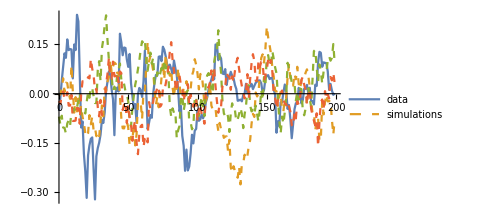
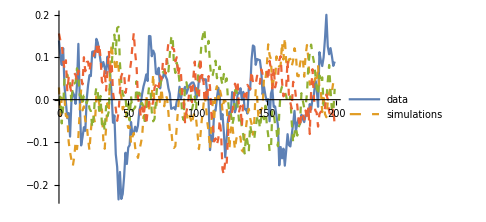
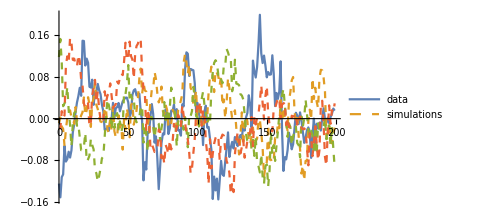
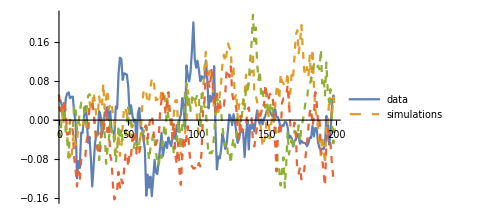
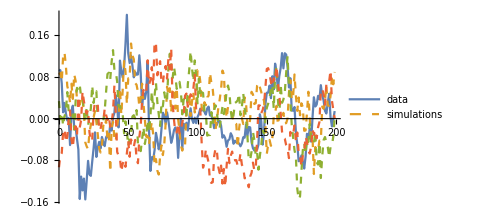
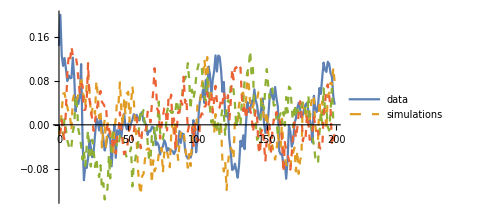

```mathematica
(* Show some simulations and data points *)
showPoints=200;
showSims=3;
Table[ListLinePlot[Join[{selNpℛsPlots[[i]][[;;showPoints]]}, selPaths[[i]][[;;showSims,;;showPoints]]],PlotStyle->{Thick, Dashed, Dashed, Dashed},PlotLegends->{"data","simulations"}, ImageSize->Medium],{i,selN}]
```

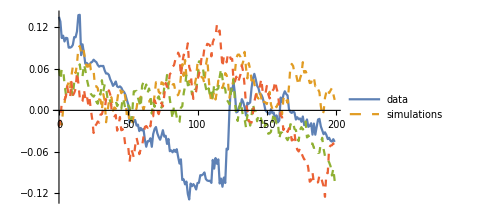
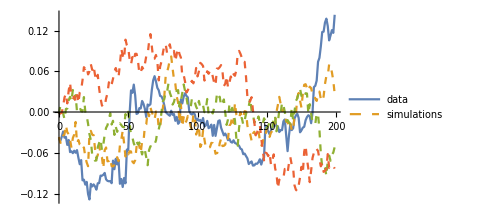
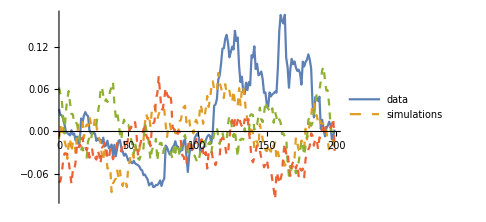
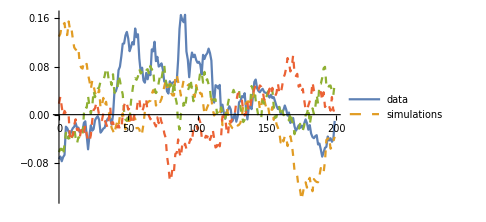
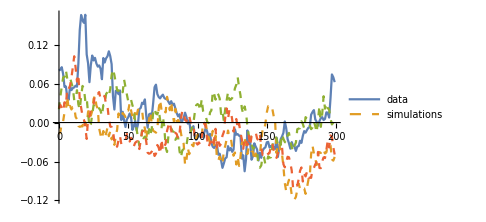
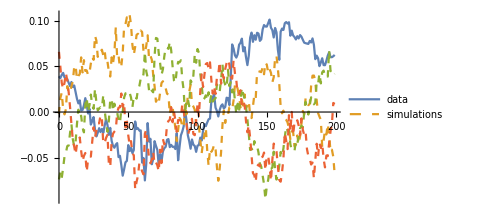
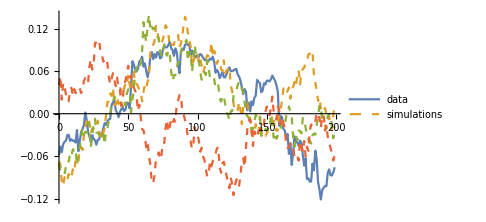
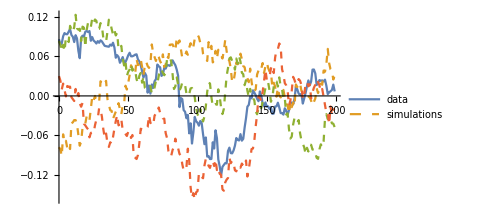

```mathematica
(* The estimated number of parameters of the sample selections fits: *)
(* From R's loess, using list of (selections) effective dfs: *)
selRInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@selBubbleScaledCsvs;
```

```mathematica
selRRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@selRInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
selRParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@selRRuns
```

{{14.9581,437.321},{15.2739,388.914},{14.9361,341.358},{15.3345,292.843},{14.8867,245.432},{15.4722,196.674}}

```mathematica
effectiveDfs
estimatedNParams
(*selEstimatedDfs=Table[Length[selBubbleScaled[[i]]]-estimatedNParams, {i, selN}]*)
selEffectiveDfs=Table[selRParams[[i]][[2]], {i, selN}]
```

437.321

14.9581

{437.321,388.914,341.358,292.843,245.432,196.674}

```mathematica
(* The "mean" RSSs (RSS/df) of the simulations: *)
selMeanRSSs=Table[Map[Total[(#[[All,2]])^2]/selEffectiveDfs[[i]]&,selPaths[[i]]], {i, selN}];(*Histogram[#, ImageSize->Medium]&/@selMeanRSSs*)
```

```mathematica
memory:=Row[{"Memory Used: ",MemoryInUse[]/1024^3.," GB"}];
Needs["Utilities`CleanSlate`"]
memory
```

Memory Used: 0.508305 GB

```mathematica
Remove[selSims]
Remove[selNpℛsPlots]
memory
```

Memory Used: 0.508397 GB

```mathematica
CleanSlate[];
memory
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 36333 Kb

Memory Used: 0.473868 GB

```mathematica
(* The standardized "mean" RSSs: *)
selStdMeanRSSs=Table[Map[#/selStdDevℛs[[i]]&,selMeanRSSs[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selStdMeanRSSs*)
```

```mathematica
(* Count *)
selCounts=Table[With[{ℛerror= ℛerrors[[i]]},Select[selMeanRSSs[[i]],#>ℛerror &]//Length],{i,selN}]
```

{1,0,0,10,2,1}

```mathematica
selPValues=Table[selCounts[[i]]/Length[selMeanRSSs[[i]]], {i, selN}]//N
```

{0.001,0.,0.,0.01,0.002,0.001}

```mathematica
selRejected=#<(1-0.95)&/@selPValues
```

{True,True,True,True,True,True}

```mathematica
(* Take the largest that is not rejected *)
largestNotRejectedIndex=Select[Table[{i,selRejected[[i]]==False},{i,selN}], #[[2]]&]//First//#[[1]]&
```

First::nofirst: {} has zero length and no first element.

{}

```mathematica
selFit={fits[[largestNotRejectedIndex]], index-> largestNotRejectedIndex}//Flatten
```

{a→2.04498,b→-1.15272,c→-0.0273549,d→0.0661394,T_1→0.412844,tc→3.659,m→0.1,ω→14.,RSS→6.69023,ℛerror→0.00311463,ℛσ→0.0557311,LL→6540.73,ρ→0.97732,σ→-0.0117994,μ→-1.79181×10^-17,index→16}

```mathematica
bestIndex=largestNotRejectedIndex
fit=fits[[bestIndex]]
```

16

{a→2.04498,b→-1.15272,c→-0.0273549,d→0.0661394,T_1→0.412844,tc→3.659,m→0.1,ω→14.,RSS→6.69023,ℛerror→0.00311463,ℛσ→0.0557311,LL→6540.73,ρ→0.97732,σ→-0.0117994,μ→-1.79181×10^-17}

```mathematica
(* Estimate tc 95% CI by Profile Likelihood *)
m=.
ω=.
tc=.
```

```mathematica
(* Do it over the best params *)
bestm=m/.fit
bestω=ω/.fit
bestTc=tc/.fit
bestLL=LL/.fit
```

0.1

14.

3.659

6540.73

```mathematica
t1=Subscript[T, 1]/.fit
```

0.412844

```mathematica
(* Selected best bubble: *)
bubbleBest=Select[bubbleScaled, #[[1]]>= t1&];
```

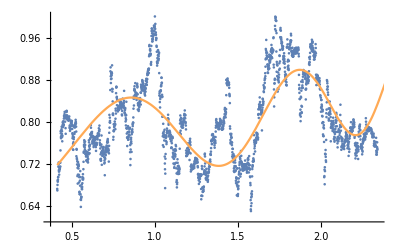

```mathematica
(* Best fit plot *)
Show[ListPlot[bubbleBest, ImageSize->Full], Plot[Evaluate[lpplsModel/.fit], {ti, t1, bestTc}, PlotStyle->{colors[[bestIndex]]}, Evaluated->True]]
```

```mathematica
(* Profile-likelihood-based 95% C.I. for Subscript[t, c]: *)
(* Get nlm function: *)
lpplsModel
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Parametrize it: *)
fit
```

{a→2.04498,b→-1.15272,c→-0.0273549,d→0.0661394,T_1→0.412844,tc→3.659,m→0.1,ω→14.,RSS→6.69023,ℛerror→0.00311463,ℛσ→0.0557311,LL→6540.73,ρ→0.97732,σ→-0.0117994,μ→-1.79181×10^-17}

```mathematica
bestLppls[x_, testTc_:bestTc]:= lpplsModel/.fit[[1;;4]]/.fit[[7;;8]]/.ti-> x/.tc-> testTc
```

```mathematica
mlℛ = Map[#[[2]]-bestLppls[#[[1]]]&, bubbleBest];
```

```mathematica
(* Fit an AR(1) process (Perhaps re-utilize / recompute the non-parametric residuals model, fitted over the selected interval): *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[mlℛ,ar1Process]
```

{ρ→0.97732,σ→-0.0117994,μ→-1.79181×10^-17}

```mathematica
bestLL==LogLikelihood[ar1Process/. estimatedAR1Model,mlℛ]
```

True

```mathematica
(* They match. *)
```

```mathematica
(* Now sligthly vary tc, and recompute residuals until the LL is 1.92 times below the max: *)
lowCItc=bestTc;
lowCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/1000;
oldSign=1;
Monitor[While[delta=bestLL-lowCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
lowCItc=lowCItc+ precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], lowCItc]&, bubbleBest];
lowCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],{delta}]
delta
{lowCItc, bestTc}
```

1.92007

{3.61388,3.659}

```mathematica
(* Let's do the upper leg of the CI: *)
highCItc=bestTc;
highCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/100;
oldSign=-1;
Monitor[While[delta=bestLL-highCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
highCItc=highCItc- precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], highCItc]&, bubbleBest];
highCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],delta]
delta
{lowCItc, bestTc, highCItc}
```

1.92002

{3.61388,3.659,3.71942}

```mathematica
(* Dates correction: *)
lastScaledTc=bubbleBest[[-1]][[1]]
```

2.3378

```mathematica
(* Now compute the equivalent date of the low CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] lowCItc/lastScaledTc]
```

Fri 18 Apr 2025 11:56:03

```mathematica
(* And the best tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] bestTc/lastScaledTc]
```

Sun 20 Apr 2025 14:25:25

```mathematica
(* And the equivalent date of the high CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] highCItc/lastScaledTc]
```

Wed 23 Apr 2025 10:02:01

```mathematica
(* With the mean tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] meanTc/lastScaledTc]
```

Tue 22 Apr 2025 15:42:03

```mathematica
(* With the max tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] maxTc/lastScaledTc]
```

Mon 12 May 2025 20:15:31

```mathematica
(* With the min tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] minTc/lastScaledTc]
```

Wed 26 Feb 2025 13:25:58

```mathematica
(* For reference: *)
{#[[5]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[5]][[2]]/lastScaledTc],#[[6]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[6]][[2]]/lastScaledTc]}&/@fits//TableForm
```

T_1→0. | Fri 1 Nov 2024 00:00:00 | tc→4.13607 | Mon 12 May 2025 20:15:31
T_1→0.0275229 | Sat 2 Nov 2024 06:47:53 | tc→4.13607 | Mon 12 May 2025 20:15:31
T_1→0.0550459 | Sun 3 Nov 2024 13:35:46 | tc→4.13607 | Mon 12 May 2025 20:15:31
T_1→0.0825688 | Mon 4 Nov 2024 20:23:40 | tc→4.13607 | Mon 12 May 2025 20:15:31
T_1→0.110092 | Wed 6 Nov 2024 03:11:33 | tc→4.13607 | Mon 12 May 2025 20:15:31
T_1→0.137615 | Thu 7 Nov 2024 09:59:26 | tc→4.13607 | Mon 12 May 2025 20:15:31
T_1→0.165138 | Fri 8 Nov 2024 16:47:20 | tc→2.52139 | Wed 26 Feb 2025 13:25:58
T_1→0.192661 | Sat 9 Nov 2024 23:35:13 | tc→2.52139 | Wed 26 Feb 2025 13:25:58
T_1→0.220183 | Mon 11 Nov 2024 06:23:07 | tc→3.7324 | Thu 24 Apr 2025 00:33:08
T_1→0.247706 | Tue 12 Nov 2024 13:11:00 | tc→3.659 | Sun 20 Apr 2025 14:25:25
T_1→0.275229 | Wed 13 Nov 2024 19:58:53 | tc→3.659 | Sun 20 Apr 2025 14:25:25
T_1→0.302752 | Fri 15 Nov 2024 02:46:47 | tc→3.659 | Sun 20 Apr 2025 14:25:25
T_1→0.330275 | Sat 16 Nov 2024 09:34:40 | tc→3.659 | Sun 20 Apr 2025 14:25:25
T_1→0.357798 | Sun 17 Nov 2024 16:22:34 | tc→3.659 | Sun 20 Apr 2025 14:25:25
T_1→0.385321 | Mon 18 Nov 2024 23:10:27 | tc→3.659 | Sun 20 Apr 2025 14:25:25
T_1→0.412844 | Wed 20 Nov 2024 05:58:20 | tc→3.659 | Sun 20 Apr 2025 14:25:25
T_1→0.440367 | Thu 21 Nov 2024 12:46:14 | tc→3.6957 | Tue 22 Apr 2025 07:29:16
T_1→0.46789 | Fri 22 Nov 2024 19:34:07 | tc→3.76909 | Fri 25 Apr 2025 17:36:59
T_1→0.495413 | Sun 24 Nov 2024 02:22:01 | tc→3.6957 | Tue 22 Apr 2025 07:29:16
T_1→0.522936 | Mon 25 Nov 2024 09:09:54 | tc→3.6957 | Tue 22 Apr 2025 07:29:16

```mathematica
(* Compute market cap at the low leg of the best Tc: *)
bestM=bestLppls[bestTc-epsilon,bestTc]
```

1.60052

```mathematica
lowCIM=bestLppls[lowCItc,bestTc]
```

1.21044

```mathematica
lastScaledM=bubbleBest[[-1]][[2]]
```

0.747206

```mathematica
lastPriceDate
```

2025-02-18

```mathematica
(* Closing market cap at lastPriceDate date (`$lastPriceDate`) (https://coinmarketcap.com/currencies/bitcoin/historical-data/https://coinmarketcap.com/currencies/bitcoin/historical-data/Nonehttps://coinmarketcap.com/currencies/bitcoin/historical-data/HyperlinkActionRecycledHyperlinkActive) (Millions of USD): *)
(* Automated download *)
timeStartTs=UnixTime[lastPriceDate];
timeEndTs=timeStartTs+86400;
latestMarketCapUrl="https://api.coinmarketcap.com/data-api/v3.1/cryptocurrency/historical?id=1&convertId=2781&timeStart="<>ToString[timeStartTs]<>"&timeEnd="<>ToString[timeEndTs]<>"&interval=1d"
```

https://api.coinmarketcap.com/data-api/v3.1/cryptocurrency/historical?id=1&convertId=2781&timeStart=1739833200&timeEnd=1739919600&interval=1d

```mathematica
latestMarketCapData=Import[latestMarketCapUrl]
```

{data→{id→1,name→Bitcoin,symbol→BTC,timeEnd→1705363199,quotes→{{timeOpen→2025-02-18T00:00:00.000Z,timeClose→2025-02-18T23:59:59.999Z,timeHigh→2025-02-18T14:26:00.000Z,timeLow→2025-02-18T19:14:00.000Z,quote→{name→2781,open→95773.8,high→96695.4,low→93388.8,close→95539.5,volume→3.732572048236×10^10,marketCap→1.89409234472463×10^12,timestamp→2025-02-18T23:59:59.999Z}}}},status→{timestamp→2025-02-19T11:50:47.249Z,error_code→0,error_message→SUCCESS,elapsed→25,credit_count→0}}

```mathematica
latestMarketCap=Flatten[latestMarketCapData[[1]][[2]][[5]][[2]]][[5]][[2]][[7]][[2]]/10^7
```

189409.234472463

```mathematica
(* Plot predicted market cap evolution (USD) :*)
fixDate[brokenDate_]:= StringTake[brokenDate,2]<>"/"<>StringTake[brokenDate,3;;]
ticksH[min_,max_]:=Table[{i,Rotate[fixDate[Block[{$DateStringFormat={"Day","Month","/","YearShort"}},DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]i/lastScaledTc]]], π/3]},{i,{t1,lastScaledTc,lowCItc, bestTc, highCItc}}]
```

```mathematica
ticksVM[min_,max_]:=Table[{i,"$ "<>ToString[IntegerPart[i latestMarketCap/Exp[lastScaledM]]]<>"M"},{i,min, max,1}]
```

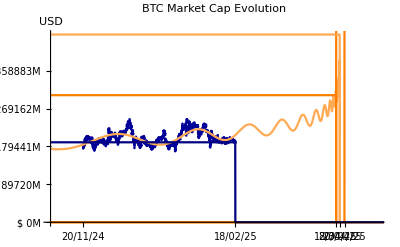

```mathematica
marketCapPrediction=Show[ListPlot[{#[[1]], Exp[#[[2]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"BTC Market Cap Evolution",PlotRange->{{0,maxTc},{0,Exp[bestM]}}, Ticks->{ticksH,ticksVM},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[Exp[lpplsModel/.fit]],UnitStep[ti-lowCItc]Exp[bestM+1],UnitStep[ti-highCItc]Exp[bestM+1]/.fit, UnitStep[lowCItc-ti]Exp[lowCIM],UnitStep[bestTc-ti]Exp[bestM],UnitStep[lastScaledTc-ti]Exp[lastScaledM]}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"BTC_MarketCapPrediction-"<>lastPriceDate<>".png",marketCapPrediction]
```

/Users/mauro/Projects/Bitcoin/BTC_MarketCapPrediction-2025-02-18.png

```mathematica
mToMarketCap[m_]:= latestMarketCap/Exp[lastScaledM] Exp[m]
```

```mathematica
lowCIMarketCap=mToMarketCap[lowCIM]
```

301011.

```mathematica
bestMarketCap=mToMarketCap[bestM]
```

444621.

```mathematica
(* The price is the ratio of the market cap (in Millions USD) to the (predicted) supply at the date: *)
mToPrice[m_, date_]:=mToMarketCap[m]10^7/supplyFunction[UnixTime[date]]
```

```mathematica
tcToDate[tc_]:= DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]tc/lastScaledTc]
```

```mathematica
(* Check: *)
lastPrice=mToPrice[lastScaledM,tcToDate[lastScaledTc]]
```

95536.7

```mathematica
lowCIPrice=mToPrice[lowCIM, tcToDate[lowCItc]]
```

149386.

```mathematica
bestPrice=mToPrice[bestM, tcToDate[bestTc]]
```

220324.

```mathematica
(* Plot predicted price evolution (USD) :*)
ticksVPrice[min_,max_]:=Table[{i,"$"<>ToString[IntegerPart[i]]},{i,min, max,50000}]
```

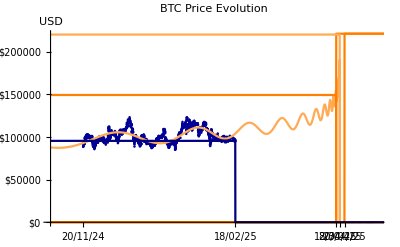

```mathematica
pricePrediction=Show[ListPlot[{#[[1]], mToPrice[#[[2]], tcToDate[#[[1]]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"BTC Price Evolution",PlotRange->{{0,maxTc},{0,bestPrice}}, Ticks->{ticksH,ticksVPrice},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[mToPrice[lpplsModel/.fit, tcToDate[ti]]],UnitStep[ti-lowCItc](bestPrice+1000),UnitStep[ti-highCItc](bestPrice+1000)/.fit, UnitStep[lowCItc-ti]lowCIPrice,UnitStep[bestTc-ti]bestPrice,UnitStep[lastScaledTc-ti]lastPrice}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/BTC_PricePrediction-"<>lastPriceDate<>".png",pricePrediction]
```

/Users/mauro/Projects/Bitcoin/png/BTC_PricePrediction-2025-02-18.png